```mathematica
Tally[Table[Factor[ChromaticPolynomial[allGraphs5[k,"graph"],x]]->allGraphs5[k,"graph"],{k,allGraphs5GeneratorAtomKeys}],First[#1]==First[#2]&]//TableForm
```

x^5→-Graphics- | 1
(-1+x)^4 x→-Graphics- | 5
(-2+x)^3 (-1+x) x→-Graphics- | 10
(-3+x)^2 (-2+x) (-1+x) x→-Graphics- | 10
(-4+x) (-3+x) (-2+x) (-1+x) x→-Graphics- | 1
(-2+x) (-1+x) x (7-5 x+x^2)→-Graphics- | 15
(-1+x) x (-7+10 x-5 x^2+x^3)→-Graphics- | 10

```mathematica
Tally[Table[ChromaticPolynomial[allGraphs5[k,"graph"],x]->allGraphs5[k,"graph"],{k,allGraphs5GeneratorAtomKeys}],First[#1]==First[#2]&]//TableForm
```

x^5→-Graphics- | 1
x-4 x^2+6 x^3-4 x^4+x^5→-Graphics- | 5
8 x-20 x^2+18 x^3-7 x^4+x^5→-Graphics- | 10
18 x-39 x^2+29 x^3-9 x^4+x^5→-Graphics- | 10
24 x-50 x^2+35 x^3-10 x^4+x^5→-Graphics- | 1
14 x-31 x^2+24 x^3-8 x^4+x^5→-Graphics- | 15
7 x-17 x^2+15 x^3-6 x^4+x^5→-Graphics- | 10

```mathematica
Tally[Table[ChromaticPolynomial[allGraphs5[k,"graph"],x]->allGraphs5[k,"graph"],{k,allGraphs5FakeAtomKeys}],First[#1]==First[#2]&]//TableForm
```

x^5→-Graphics- | 1
-x^4+x^5→-Graphics- | 10
24 x-50 x^2+35 x^3-10 x^4+x^5→-Graphics- | 1
-6 x^2+11 x^3-6 x^4+x^5→-Graphics- | 5
2 x^3-3 x^4+x^5→-Graphics- | 10
-2 x^2+5 x^3-4 x^4+x^5→-Graphics- | 10
x^3-2 x^4+x^5→-Graphics- | 15

```mathematica
Tally[Table[Factor[ChromaticPolynomial[allGraphs5[k,"graph"],x]]->allGraphs5[k,"graph"],{k,allGraphs5FakeAtomKeys}],First[#1]==First[#2]&]//TableForm
```

x^5→-Graphics- | 1
(-1+x) x^4→-Graphics- | 10
(-4+x) (-3+x) (-2+x) (-1+x) x→-Graphics- | 1
(-3+x) (-2+x) (-1+x) x^2→-Graphics- | 5
(-2+x) (-1+x) x^3→-Graphics- | 10
(-2+x) (-1+x)^2 x^2→-Graphics- | 10
(-1+x)^2 x^3→-Graphics- | 15

```mathematica
Table[Factor[ChromaticPolynomial[allGraphs5[k,"graph"],x]],{k,allGraphs5FakeAtomKeys}]//Tally//TableForm
```

x^5 | 1
(-1+x) x^4 | 10
(-4+x) (-3+x) (-2+x) (-1+x) x | 1
(-3+x) (-2+x) (-1+x) x^2 | 5
(-2+x) (-1+x) x^3 | 10
(-2+x) (-1+x)^2 x^2 | 10
(-1+x)^2 x^3 | 15

```mathematica
Table[allGraphs5[k,"graph"]->allGraphs5[k,"colofourgenerator"]/.RepGraph["G"],{k,alfa1s}]//TableForm
```

-Graphics-→-Graphics-228820--Graphics-294430--Graphics-229630+-Graphics-295240
-Graphics-→-Graphics-273100--Graphics-294970--Graphics-273370+-Graphics-295240
-Graphics-→-Graphics-294400--Graphics-295210--Graphics-294430+-Graphics-295240
-Graphics-→-Graphics-229360--Graphics-294970--Graphics-229630+-Graphics-295240
-Graphics-→-Graphics-273340--Graphics-295210--Graphics-273370+-Graphics-295240

```mathematica
Table[allGraphs5[k,"graph"]->allGraphs5[k,"colofourgenerator"],{k,quads}]//TableForm
```

-Graphics-→g13x2x4x5-g1x2x3x4x5
-Graphics-→g1x24x3x5-g1x2x3x4x5
-Graphics-→g1x2x35x4-g1x2x3x4x5
-Graphics-→g14x2x3x5-g1x2x3x4x5
-Graphics-→g1x25x3x4-g1x2x3x4x5

```mathematica
repQuad=Table[(allGraphs5[k,"colofourgenerator"]/.g1x2x3x4x5->0)->allGraphs5[k,"graph"],{k,quads}]
```

{g13x2x4x5→-Graphics-,g1x24x3x5→-Graphics-,g1x2x35x4→-Graphics-,g14x2x3x5→-Graphics-,g1x25x3x4→-Graphics-}

```mathematica
Table[allGraphs5[k,"graph"]->(allGraphs5[k,"colofourgenerator"]/.g1x2x3x4x5->0/.repQuad)/.RepGraph["G"],{k,alfa1s}]//TableForm
```

-Graphics-→--Graphics---Graphics-+-Graphics-228820
-Graphics-→--Graphics---Graphics-+-Graphics-273100
-Graphics-→--Graphics---Graphics-+-Graphics-294400
-Graphics-→--Graphics---Graphics-+-Graphics-229360
-Graphics-→--Graphics---Graphics-+-Graphics-273340

```mathematica
Table[allGraphs5[k,"graph"]->allGraphs5[k,"colofourgenerator"]/.g1x2x3x4x5->0/.RepGraph["G"],{k,quads}]//TableForm
```

-Graphics-→-Graphics-229630
-Graphics-→-Graphics-294430
-Graphics-→-Graphics-295210
-Graphics-→-Graphics-273370
-Graphics-→-Graphics-294970

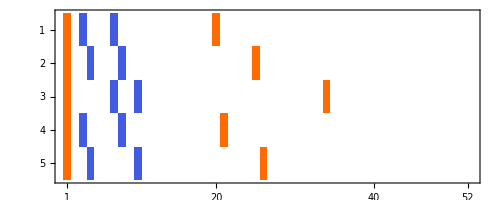

```mathematica
Table[BaseCoeff[k,"G"],{k,alfa1s}]//MatrixPlot
```

```mathematica
Map[First,repQuad]
```

{g13x2x4x5,g1x24x3x5,g1x2x35x4,g14x2x3x5,g1x25x3x4}

```mathematica
Table[Solve [allGraphs5[k,"graph"]==(allGraphs5[k,"colofourgenerator"]/.g1x2x3x4x5->0),g13x2x4x5],{k,alfa1s}]//TableForm
```

g13x2x4x5→--Graphics-+g13x24x5-g1x24x3x5


g13x2x4x5→--Graphics-+g13x25x4-g1x25x3x4

```mathematica
g13x2x4x5->--Graphics-+g13x25x4-g1x25x3x4/.g13x2x4x5->--Graphics-+g13x24x5-g1x24x3x5/.repQuad
```

--Graphics---Graphics-+g13x24x5→--Graphics---Graphics-+g13x25x4

```mathematica
repZero=Table[allGraphs5[k,"colofour"]->0,{k,alfa1s}]
```

{v13x24x5→0,v14x25x3→0,v1x24x35→0,v13x25x4→0,v14x2x35→0}

```mathematica
Solve[Table[allGraphs5[k,"colofour"]==(allGraphs5[k,"colofourgenerator"]/.g1x2x3x4x5->0),{k,alfa1s}],Map[First,repQuad]]/.repQuad/.RepGraph["G"]/.repZero/.RepGraph["C"]//First//TableForm
```

-Graphics-→1/2 (--Graphics-294400+-Graphics-273340--Graphics-273100+-Graphics-229360+-Graphics-228820)
-Graphics-→1/2 (-Graphics-294400--Graphics-273340+-Graphics-273100--Graphics-229360+-Graphics-228820)
-Graphics-→1/2 (-Graphics-294400+-Graphics-273340--Graphics-273100+-Graphics-229360--Graphics-228820)
-Graphics-→1/2 (--Graphics-294400+-Graphics-273340+-Graphics-273100--Graphics-229360+-Graphics-228820)
-Graphics-→1/2 (-Graphics-294400--Graphics-273340+-Graphics-273100+-Graphics-229360--Graphics-228820)